```mathematica
xdot1[u_, x_, y_]= u*x-3y-x^3
ydot1[u_, x_, y_]= 3x+u*y+2y^3
xdot2[u_, x_, y_]= u*x+y-x^2
ydot2[u_, x_, y_]= -x+u*y+2x^2
```

x-x^3-3 y

3 x+y+2 y^3

x-x^2+y

-x+2 x^2+y

```mathematica
u = 0
```

0

```mathematica
xdot1
```

xdot1

```mathematica
xdot1[u,x,y]
```

u x-x^3-3 y

```mathematica
Unset[u]
```

```mathematica
Unset[x]
```

```mathematica
f1 = -x^3
g1 = 2y^3
f2 = -x^2
g2 = 2x^2
```

-x^3

2 y^3

-x^2

2 x^2

```mathematica
D[g2,{y,1}]
```

0

```mathematica
u = 0
```

-1

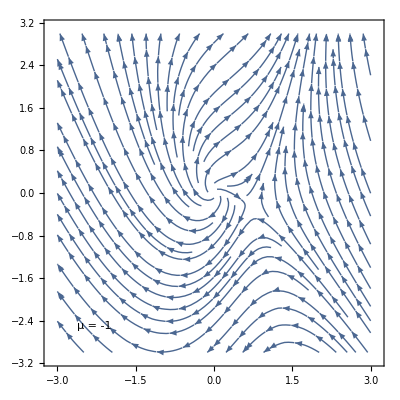

```mathematica
u=-1
text = Graphics[Text["μ = -1",{-2.3, -2.5}]];
plot = StreamPlot[{xdot2[u,x,y], ydot2[u, x,y ]},{x,-3,3},{y,-3,3}];
Show[plot, text]
```

```mathematica
xdot1
```

xdot1

```mathematica
xdot1[u]
```

ux-x^3-3 y